```mathematica
PtxZero = 10^-2;
Ptxi =10^-3;
a=4;
rD = 130;
rZero = 60;
rZeroD = 80;
n = 10^-11;
vZeroD=1;
vD=1;
vZero=1;
```

```mathematica
hZeroD=PtxZero/(rZeroD^a);
hD= Ptxi/(rD^a);
hZero = Ptxi/(rZero^a);
beta = (vZeroD*hZeroD)/(vD *hD);
```

```mathematica
gamma =0.2
```

0.2

```mathematica
Pd= Exp[-(gamma *n)/(vD *hD)];
PZero=Exp[-(gamma *n)/(vZero *hZero)];
G=10^(-10);
q=0.1;
qZero = 0.95
nUsers=50;
```

0.95

```mathematica
PZeroiZero[i_]:=PZero(1/(1+gamma))^(i-1)
```

```mathematica
PZeroiOne[i_]:= PZeroiZero[i](1+gamma* rZero^a* G)^-1
```

```mathematica
PDiZero[i_]:=Pd*(1/(1+gamma))^(i-1)
```

```mathematica
PDiOne[i_]:=PDiZero[i]/(1+(beta *gamma))
```

```mathematica
PZeroD[i_]:=Exp[-(gamma* n)/(vZero* hZero)](1/(1+gamma/beta))^i
```

```mathematica
rZeroF[k_,PrxOn_] :=PrxOn*∑_(i=k)^nUsers Binomial[  nUsers,i]*Binomial[i,k]*q^i *(1-q)^( nUsers-i)*PZeroiZero[i]^k*(1-PDiZero[i])^k*(1-PZeroiZero[i]*(1-PDiZero[i]))^(i-k)
rOneF[k_,PrxOn_, PtxOn_] := PrxOn*((1-qZero*PtxOn)*∑_(i=k)^nUsers Binomial[nUsers,i] *Binomial[i, k]*q^i *(1-q)^(nUsers-i)*PZeroiZero[i]^k*(1-PDiZero[i])^k*(1-PZeroiZero[i]*(1-PDiZero[i]))^(i-k)+ qZero*PtxOn*∑_(i=k)^nUsers Binomial[nUsers,i]*Binomial[i, k]*q^i *(1-q)^(nUsers-i)*PZeroiOne[i]^k*(1-PDiOne[i])^k*(1-PZeroiOne[i]*(1-PDiOne[i]))^(i-k))
```

```mathematica
pQueueDecreasedByOne[ PtxOn_] :=  qZero*PtxOn*∑_(k=0)^nUsers Binomial[nUsers,k] q^k *(1-q)^(nUsers-k)PZeroD[k]*(1-PZeroiOne[k](1-PDiOne[k]))^k
```

```mathematica
pQueueInreasedByOne[k_,PrxOn_, PtxOn_] :=PrxOn*((1-qZero*PtxOn)∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)PZeroiZero[i]^k (1-PDiZero[i])^k(1-PZeroiZero[i](1-PDiZero[i]))^(i-k)+qZero*PtxOn*∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)(1- PZeroD[i])PZeroiOne[i]^k(1-PDiOne[i])^k(1-PZeroiOne[i](1-PDiOne[i]))^(i-k)+qZero*PtxOn*∑_(i=k+1)^nUsers Binomial[nUsers,i] Binomial[i, k+1] q^i*(1-q)^(nUsers-i) PZeroD[i] PZeroiOne[i]^(k+1)(1-PDiOne[i])^(k+1)(1-PZeroiOne[i](1-PDiOne[i]))^(i-k-1))
```

```mathematica
pQueueInreasedByOneWhenZero[PrxOn_, PtxOn_] := 1-pQueueDecreasedByOne[ PtxOn]-∑_(i=1)^nUsers pQueueInreasedByOne[i,PrxOn, PtxOn]
```

```mathematica
pQueueInreasedByZero[k_, PrxOn_]:=PrxOn*∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)PZeroiZero[i]^k *(1-PDiZero[i])^k*(1-PZeroiZero[i](1-PDiZero[i]))^(i-k)
```

```mathematica
lambdaZero[PrxOn_]:=∑_(k=1)^nUsers k  *rZeroF[k,PrxOn]
```

```mathematica
lambdaOne[PrxOn_, PtxOn_]:=∑_(k=1)^nUsers k* rOneF[k,PrxOn, PtxOn]
```

```mathematica
probQueueIsEmpty [PrxOn_, PtxOn_] :=(pQueueDecreasedByOne[ PtxOn] -∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] )/(pQueueDecreasedByOne[ PtxOn]-(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn])+lambdaZero [PrxOn])
probQueueIsEmpty [1, 0.5]
```

-7.09112

```mathematica
avgQueueLength [PrxOn_, PtxOn_] :=1/(2(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] -pQueueDecreasedByOne[PtxOn] )(pQueueDecreasedByOne[PtxOn]-(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn])+lambdaZero [PrxOn]))((∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] -pQueueDecreasedByOne[PtxOn] )(∑_(i=1)^nUsers i *(i+3)*pQueueInreasedByZero[i, PrxOn])+lambdaZero[PrxOn](2pQueueDecreasedByOne[ PtxOn]-∑_(i=1)^nUsers i *(i+3)*pQueueInreasedByOne[i,PrxOn, PtxOn]))
```

```mathematica
ThroughputDirect [PrxOn_,PtxOn_]:= (qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn])* ∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)*PDiOne[k+1])+((1-qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]))*∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)*PDiZero[k+1])
```

```mathematica
ThroughputRelay[PrxOn_, PtxOn_] := PrxOn*((qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]) *(∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)* (1-PDiOne[k+1])*PZeroiOne[k+1]))+( (1-qZero* PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn])) *(∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k) *(1-PDiZero[k+1])*PZeroiZero[k+1])))
```

```mathematica
serviceRate[PtxOn_]:= PtxOn*∑_(k=0)^nUsers Binomial[nUsers,k]*qZero *q^k*(1-q)^(nUsers-k)*PZeroD[k]
```

```mathematica
(*Plot[serviceRate[p],{p,0,1}]*)
```

```mathematica
arrivalRate[PrxOn_, PtxOn_]:=  (lambdaZero[PrxOn] *PtxOn*probQueueIsEmpty[PrxOn, PtxOn] + PrxOn*(1-PtxOn ))+(lambdaOne[PrxOn, PtxOn]* PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]))

arrivalRateNEW[PrxOn_, PtxOn_]:=  (lambdaZero[PrxOn] *probQueueIsEmpty[PrxOn, PtxOn] )+ (lambdaOne[PrxOn, PtxOn]* (1-probQueueIsEmpty[PrxOn, PtxOn]))
```

```mathematica
(*Plot3D[arrivalRate[Rx,Tx],{Rx,0,1},{Tx,0,1},AxesLabel->Automatic]*)
```

```mathematica
(*Plot3D[arrivalRateNEW[Rx,Tx],{Rx,0,1},{Tx,0,1},AxesLabel->Automatic]*)
```

```mathematica
nUsers
```

50

```mathematica
(*NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]≥ arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}]*)
```

```mathematica
(*gamma*)
```

```mathematica
TableForm[ results= Table[
{nUsers,Values[ NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],(serviceRate[PtxOn] ≥ arrivalRateNEW[PrxOn, PtxOn] + 10^(-3))&&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[2]] ][[1]],
Values[ NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],(serviceRate[PtxOn] ≥ arrivalRateNEW[PrxOn, PtxOn] + 10^(-3)) &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[2]] ][[2]],

NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],(serviceRate[PtxOn] ≥ arrivalRateNEW[PrxOn, PtxOn] + 10^(-3))&&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[1]]
}, 
{nUsers,50} ] ];
```

```mathematica
TableForm[results,TableHeadings->{None,{"# Users","P(Tx=on)","P(Rx=on)","throughput/user"}}]
```

# Users | P(Tx=on) | P(Rx=on) | throughput/user
1 | 0.993775 | 1. | 0.0988235
2 | 0.993775 | 1. | 0.0978025
3 | 0.993775 | 1. | 0.0966921
4 | 0.993775 | 1. | 0.095487
5 | 0.993775 | 1. | 0.0941819
6 | 0.993775 | 1. | 0.092772
7 | 0.993775 | 1. | 0.0912527
8 | 0.993775 | 1. | 0.0896205
9 | 0.993775 | 1. | 0.0878724
10 | 0.995959 | 1. | 0.0860066
11 | 0.995959 | 1. | 0.0840223
12 | 0.035869 | 0. | 0.0469495
13 | 0.035869 | 0. | 0.046167
14 | 0.035869 | 0. | 0.0453975
15 | 0.00549069 | 0. | 0.0446409
16 | 0.00549069 | 0. | 0.0438969
17 | 0.00549069 | 0. | 0.0431653
18 | 0.00549069 | 0. | 0.0424459
19 | 0.00549069 | 0. | 0.0417384
20 | 0.00549069 | 0. | 0.0410428
21 | 0.00549069 | 0. | 0.0403587
22 | 0.00549069 | 0. | 0.0396861
23 | 0.00549069 | 0. | 0.0390247
24 | 0.00549069 | 0. | 0.0383742
25 | 0.00549069 | 0. | 0.0377347
26 | 0.00549069 | 0. | 0.0371058
27 | 0.00549069 | 0. | 0.0364873
28 | 0.00549069 | 0. | 0.0358792
29 | 0.00549069 | 0. | 0.0352812
30 | 0.00549069 | 0. | 0.0346932
31 | 0.0054907 | 0. | 0.034115
32 | 0.00549069 | 0. | 0.0335464
33 | 0.0054907 | 0. | 0.0329873
34 | 0.0054907 | 0. | 0.0324375
35 | 0.00549065 | 0. | 0.0318969
36 | 1. | 0. | 0.0313653
37 | 1. | 0. | 0.0308425
38 | 1. | 0. | 0.0303285
39 | 1. | 0. | 0.029823
40 | 1. | 0. | 0.0293259
41 | 1. | 0. | 0.0288372
42 | 1. | 0. | 0.0283566
43 | 1. | 0. | 0.0278839
44 | 1. | 0. | 0.0274192
45 | 1. | 0. | 0.0269622
46 | 1. | 0. | 0.0265129
47 | 1. | 0. | 0.026071
48 | 1. | 0. | 0.0256365
49 | 1. | 0. | 0.0252092
50 | 1. | 0. | 0.024789

```mathematica
(*ListPointPlot3D[Table[ThroughputDirect[Rx,Tx],{Rx,0.01,1.0,0.01},{Tx,0.01,1.0,0.01}]]*)
```

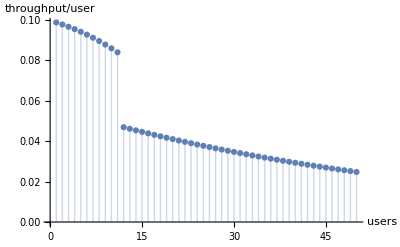

```mathematica
usersIdx=Table[results[[i,1]],{i,1,50}];
TxON = Table[results[[i,2]],{i,1,50}];RxON = Table[results[[i,3]],{i,1,50}];
perUserThroughput=Table[results[[i,4]],{i,1,50}];
ListPlot[Table[{usersIdx[[i]],perUserThroughput[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, throughput/user}]

(*avgQueueLength[TxON,RxON]*)
```

```mathematica
(*ListPlot[avgQueueLength[TxON,RxON],Filling->Axis, AxesLabel->{ users, "avg. queue size"}]*)
G
gamma
```

1/10000000000

0.2

```mathematica
perUserThroughput
```

{0.0988235,0.0978025,0.0966921,0.095487,0.0941819,0.092772,0.0912527,0.0896205,0.0878724,0.0860066,0.0840223,0.0469495,0.046167,0.0453975,0.0446409,0.0438969,0.0431653,0.0424459,0.0417384,0.0410428,0.0403587,0.0396861,0.0390247,0.0383742,0.0377347,0.0371058,0.0364873,0.0358792,0.0352812,0.0346932,0.034115,0.0335464,0.0329873,0.0324375,0.0318969,0.0313653,0.0308425,0.0303285,0.029823,0.0293259,0.0288372,0.0283566,0.0278839,0.0274192,0.0269622,0.0265129,0.026071,0.0256365,0.0252092,0.024789}

```mathematica
qZero
```

0.95

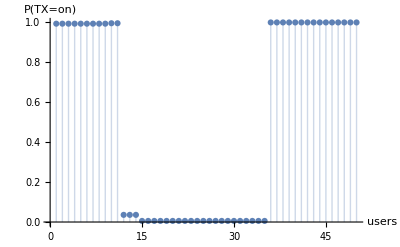

```mathematica
ListPlot[Table[{usersIdx[[i]],TxON[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, "P(TX=on)"}]
```

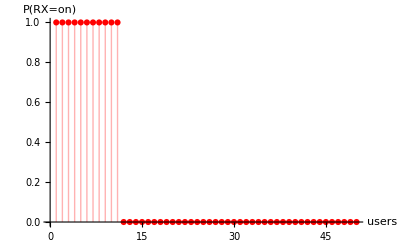

```mathematica
ListPlot[Table[{usersIdx[[i]],RxON[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, "P(RX=on)"},PlotStyle->{Red,Thick}]
```

```mathematica
gamma
```

0.2

```mathematica
TxON
```

{0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.995959,0.995959,0.035869,0.035869,0.035869,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.00549069,0.0054907,0.00549069,0.0054907,0.0054907,0.00549065,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
RxON
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
G
```

1/10000000000